# Quantum Arithmetic

We will discuss quantum circuits for arithmetic, focusing on the Quantum Fourier Transform, and show how it enables quantum addition and multiplication.

## Key Concepts

Quantum Fourier Transform

Phase Basis

## The Discrete Fourier Transform

The discrete Fourier transform is a mathematical transformation that is very useful in processing data. It has many applications and is often employed when one wants to analyze signals over time.

This transformation on a list of n numbers is given by the so-called Fourier matrix of size n. For example, the Fourier matrix of size 4 looks like:

```mathematica
FourierMatrix[4]//MatrixForm
```

(1/2 | 1/2 | 1/2 | 1/2
1/2 | ⅈ/2 | -1/2 | -ⅈ/2
1/2 | -1/2 | 1/2 | -1/2
1/2 | -ⅈ/2 | -1/2 | ⅈ/2)

Recall that quantum states of n qubits can be represented by a list of 2^n complex amplitudes. For example, 8 complex amplitudes describe 3 qubits:

```mathematica
ψ=QuantumState["RandomPure"[3]];
ψ["StateVector"]//MatrixForm
```

(0.413933-0.014112 ⅈ
-0.493966+0.032013 ⅈ
0.0940398-0.116863 ⅈ
-0.263557+0.283288 ⅈ
-0.240619+0.206365 ⅈ
0.226864-0.12574 ⅈ
-0.152504-0.019467 ⅈ
-0.164081-0.439201 ⅈ)

The most naive way to implement the classical discrete fourier transform on a list of 2^n complex data points requires O(2^(2n)) operations. However, there are other methods known as Fast Fourier Transforms. These faster methods only require O(n 2^n) classical operations. Because 2^n complex data points can be encoded in only n qubits, the quantum Fourier transform requires only O(n^2) quantum gates to be applied to these n qubits.

The Quantum Fourier Transform maps an n-qubit computational-basis state to a uniform superposition whose phases encode the original index in Fourier order:

QFTx=1/(√(2^n))∑_(y=0)^(2^n-1) ⅇ^(2π ⅈ xy/2^n)y with 0<=x<=2^n-1

Show the effect of QFT on a symbolic 2-qubit state:

```mathematica
MatrixForm[Array[Subscript[c, ##]&,2^2]]->MatrixForm@FullSimplify@Normal@QuantumCircuitOperator["Fourier"[2]][QuantumState[Array[Subscript[c, ##]&,2^2]]]["StateVector"]
```

(c_1
c_2
c_3
c_4)→(1/2 (c_1+c_2+c_3+c_4)
1/2 (c_1+ⅈ (c_2+ⅈ c_3-c_4))
1/2 (c_1-c_2+c_3-c_4)
1/2 (c_1-ⅈ c_2-c_3+ⅈ c_4))

Of course, you can also implement this directly with matrix operations on the state vector:

```mathematica
MatrixForm@FullSimplify[FourierMatrix[4].Array[Subscript[c, ##]&,2^2]]
```

(1/2 (c_1+c_2+c_3+c_4)
1/2 (c_1+ⅈ (c_2+ⅈ c_3-c_4))
1/2 (c_1-c_2+c_3-c_4)
1/2 (c_1-ⅈ c_2-c_3+ⅈ c_4))

The circuit to implement a 3-qubit QFT is given below:

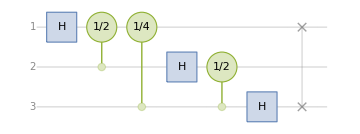

```mathematica
QuantumCircuitOperator["Fourier"[3]]["Diagram"]
```

Note the SWAP operation at the end; these are present so that the operator’s matrix elements are identical to the Fourier matrix of the appropriate size. Depending on the conventions for encoding the classical information, the SWAP operations may or may not appear in other texts.

```mathematica
QuantumCircuitOperator["Fourier"[3]]["Matrix"]==FourierMatrix[2^3]
```

True

The Fourier transform of a state vector is equivalent to the QFT action on the corresponding state:

```mathematica
Fourier[ψ["StateVector"]]==QuantumCircuitOperator["Fourier"[3]][ψ]["StateVector"]
```

True

The inverse Fourier transform is equivalent to inverse of QFT:

```mathematica
InverseFourier[ψ["StateVector"]]==QuantumCircuitOperator["InverseFourier"[3]][ψ]["StateVector"]
```

True

Show the diagram of inverse QFT:

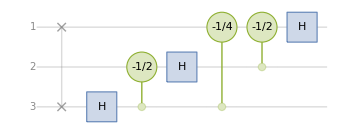

```mathematica
QuantumCircuitOperator["InverseFourier"[3]]["Diagram"]
```

## Phase Basis Encoding

As we discussed before, the computational basis is not the only way to encode classical information in a quantum state. Recall that the relative phase between two states can be experimentally distinguished. Thus, even if two states have the same probability to obtain outcomes in the computational basis, they are not the same state and will give different probabilities for outcomes in some other basis.

Consider two states who only differ by a relative phase difference between computational basis states:

```mathematica
ψ1=QuantumState["UniformSuperposition"];
ψ2=QuantumOperator["Phase"[θ]]@ψ1;
```

Although these two states are different, the probabilities in the computational basis are identical:

```mathematica
Simplify[ψ1["ProbabilitiesList"]==ψ2["ProbabilitiesList"],θ∈Reals]
```

True

However, the state really does change due to the phase rotation. You can see the effect in the Bloch plot below:

```mathematica
With[{ψ=QuantumCircuitOperator[{"UniformSuperposition","Phase"[phase]},"Parameters"->phase][]},
Manipulate[ψ[θ]["BlochPlot",PlotLabel->"θ_phase = "<>ToString@θ],{θ,0,2Pi},ControlPlacement->Top,TrackedSymbols:>θ,Initialization:>Needs["Wolfram`QuantumFramework`"]]
]
```

With this in mind, consider the following circuit:

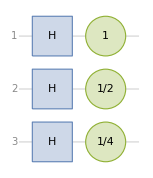

```mathematica
QuantumCircuitOperator["PhaseNumber"[1,3]]["Diagram"]
```

This is a circuit that encodes a number in n-qubit. In this case, 1 is encode in 3-qubits (in the base-2 it means):

```mathematica
IntegerDigits[1,2,3]
```

{0,0,1}

But how do you "read out" this phase information if all the measurements are performed in the computational basis? If you simply try to measure, the information encoded in the qubit phases is lost.

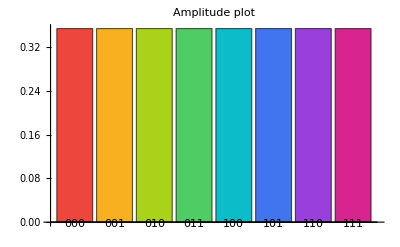

```mathematica
QuantumCircuitOperator["PhaseNumber"[1,3]][]["AmplitudesChart",ChartLegends->Automatic,PlotLabel->"Amplitude plot"]
```

As you can see from the changing colors in the above plot, the information of the input state is transferred to information about the relative phases of each qubit (with respect to a uniform superposition in the computational basis). But that information is not accessible if measuring in the computational basis:

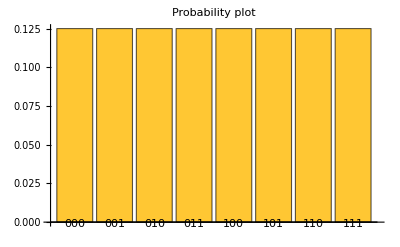

```mathematica
QuantumCircuitOperator["PhaseNumber"[1,3]][]["ProbabilitiesPlot",PlotLabel->"Probability plot"]
```

As you can see from the plot, the phase information is not immediately accessible in the computational basis. Instead, you must perform the inverse of the quantum fourier transform, and then measure.

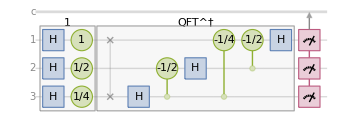

```mathematica
QuantumCircuitOperator[{"PhaseNumber"[1,3],"InverseFourier"[3],"M"->Range[3]}]["Diagram"]
```

By performing the inverse quantum Fourier transform, all of the phase information is now encoded in the computational basis. The measurement outcome is now the same as the number which was encoded in the phase basis:

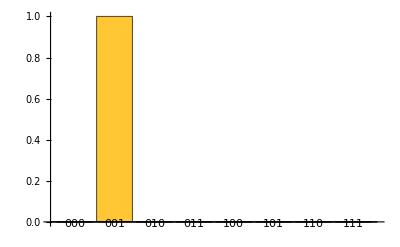

```mathematica
QuantumCircuitOperator[{"PhaseNumber"[1,3],"InverseFourier"[3],"M"->Range[3]}][]["ProbabilitiesPlot"]
```

With knowledge of the phase basis and the quantum fourier transform, you are now in a position to implement quantum circuits that carry out arithmetic. Note that the final outcome {0,0,1} is the same as base-2 of the number 1 encoded in 3-qubits

```mathematica
IntegerDigits[1,2,3]
```

{0,0,1}

## Quantum Phase Adders

When designing quantum circuits for arithmetic, it is important to distinguish between a circuit which performs the computation in-place as opposed to in a register. The in-place operation uses the same number of qubits as the input, but those qubits no longer encode the original input. In contrast, using a register requires more qubits to store the result, but the original qubits will still typically encode the original input when the algorithm is done.

As an example, let’s say you want to build a circuit which adds three to your input. This can be done using the pre-named "PhaseNumber" family of circuits. As with any digital computation, the arithmetic is performed modulo N, where N is the number of bits (or in this case qubits) used.

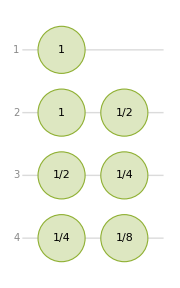

```mathematica
QuantumCircuitOperator["PhaseNumber"[3,4,False],"Add(3)"]["Diagram",ImageSize->Small]
```

Let’s use this to compute 12+3 using four qubits:

```mathematica
qc1=With[{n=4},
QuantumCircuitOperator[{QuantumState[IntegerString[12,2,n],"Label"->12],"Fourier"[n],QuantumCircuitOperator["PhaseNumber"[3,n,False],"Add(3)"],"InverseFourier"[n],"M"->Range[n]}]
];
```

This circuit first performs a quantum Fourier transform to get the input information into the phase basis, then applies an operation to add 3 in the phase basis, then performs an inverse quantum Fourier transform, and finally measures the results:

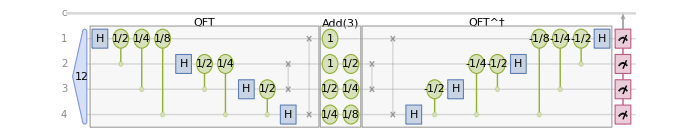

```mathematica
qc1["Diagram",ImageSize->700]
```

Find the measurement probabilities:

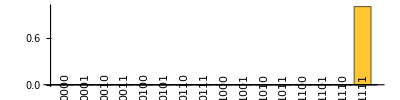

```mathematica
qc1[]["ProbabilitiesPlot","LabelsAngle"->90Degree,AspectRatio->1/4]
```

Given the outcome with maximum probability, determine the corresponding integer (using the bitstring-to-integer mapping):

```mathematica
FromDigits[Keys[Sort[qc1[]["Probability"]]][[-1]]["Name"],2]
```

15

With probability 1, this circuit gives the state corresponding to 15, the correct result for 12+3.

Note that with this kind of in-place operation, the circuit can only add 3 to the inputs. It cannot add any other number without changing the gates. However, it is possible for the input to be a superposition of states.

For example, suppose you didn’t know whether you wanted your input to be 6 or 4. You can run both computations at the same time using the previous type of circuit:

```mathematica
ψInputSuperposition=QuantumState[QuantumState["0110"]+QuantumState["0100"],"Label"->"ψ_6+ψ_4"]["Normalize"];
ψInputSuperposition["Formula"]
```

1/(√2)0100+1/(√2)0110

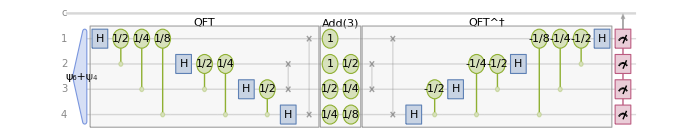

```mathematica
qc2=QuantumCircuitOperator[{ψInputSuperposition,"Fourier"[4],addThree[4],"InverseFourier"[4],"M"->Range[4]}];
qc2["Diagram",ImageSize->700]
```

Since the input was a superposition of states corresponding to 4 and 6, the output will now be a superposition of states corresponding to 7 and 9:

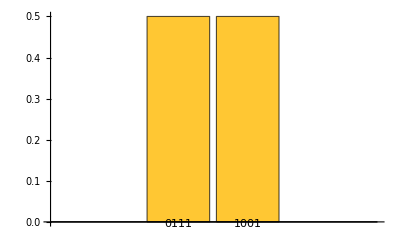

```mathematica
N[qc2][]["ProbabilityPlot"]
```

## Arbitrary Addition

While a circuit that can add superpositions of numbers to a specific number is already useful for quantum parallelization, you might instead be interested to have a circuit with fixed gates which can add any numbers between 0 and 2^n. This can be implemented as follows:

```mathematica
ClearAll[adderBlock]
adderBlock[n_Integer/;n>0]:=
QuantumCircuitOperator[
Table["C"[Table["PhaseShift"[1+a-b]->2n+1-b,{b,a}],{a}],{a,n}],
"Σ"
]
```

As before, the quantum Fourier transform and inverse quantum Fourier transform are utilized as part of the full circuit:

```mathematica
ClearAll[qftAdder]
qftAdder[n_Integer/;n>0]:=
QuantumCircuitOperator[{
"Fourier"[n]->Range[n+1,2 n],
adderBlock[n],
"InverseFourier"[n]->Range[n+1,2 n]
}]
```

A circuit to add 2+2 would then look like this:

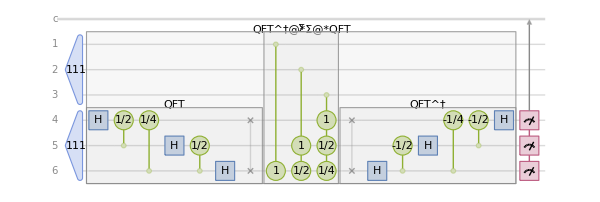

```mathematica
qc3=QuantumCircuitOperator[{
"111"->{1,2,3},
"111"->{4,5,6},
QuantumCircuitOperator[qftAdder[3]],
"M"->{4,5,6}
}];
qc3["Diagram",ImageSize->600,Expand->2]
```

With probability 1, the measured outcome of this circuit gives the state corresponding to 4 when the input states both correspond to 2.

```mathematica
qc3[]["Probability"]
```

<|110→1|>

Recall the binAdd function from the first lecture; we can use it to verify the result.

```mathematica
binAdd["101","111"]
```

1100

## Circuits for Multiplication

Multiplication can be achieved through repeated addition. When multiplying two numbers representable with n bits, the result can always be represented with 2n bits. Since you are now working with a larger register, you can be more efficient with gates by introducing a circuit element that has the effect of adding not just an input, but adding 2^k times that input.

You could define such a circuit element as follows:

```mathematica
Clear[kAdderBlock]
```

```mathematica
kAdderBlock[n_Integer,Optional[k_Integer,0]]/;n>0&&n>=k>=0:=
QuantumCircuitOperator[
Table["C"[Table["PhaseShift"[1+n+a-b-k]->3n+1-b,{b,a+n-k}],{a}],{a,n}],
StringTemplate["2^(`k`)Σ"][<|"k"->k|>]]
```

A circuit to add 2+4×2 would then look like this:

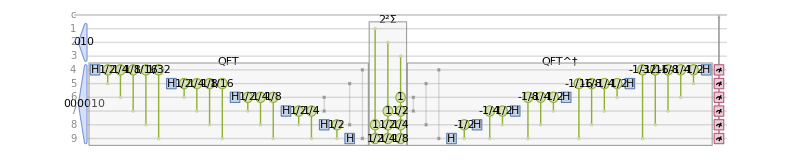

```mathematica
qc4=QuantumCircuitOperator[{
"010"->{1,2,3},
"000010"->{4,5,6,7,8,9},
"Fourier"[6]->{4,5,6,7,8,9},
kAdderBlock[3,2],
"InverseFourier"[6]->{4,5,6,7,8,9},
"M"->{4,5,6,7,8,9}
}];
qc4["Diagram",ImageSize->800,Expand->2]
```

As expected, 2+4×2=10, represented in binary:

```mathematica
N[qc4][]["Probability"]
```

<|001010→1.|>

Which is what we expected:

```mathematica
IntegerDigits[10,2,6]
```

{0,0,1,0,1,0}

A multiplication circuit would then use these blocks, controlled by bits from another register. A possible implementation looks like this:

```mathematica
Clear[mulBlock]
```

```mathematica
mulBlock[n_Integer]/;n>0:=
QuantumCircuitOperator[
Flatten@Table["C"[Table["PhaseShift"[1+i1+i2-r]->4n+1-r,{r,i1+i2}],{i1,i2+n}],{i1,n},{i2,n}],
"Π"]
```

```mathematica
Clear[qftMul]
```

```mathematica
qftMul[n_Integer]/;n>0:=
QuantumCircuitOperator[{
"Fourier"[2n]->Range[2n+1,4n],
mulBlock[n],
"InverseFourier"[2n]->Range[2n+1,4n]
},"QFT Multiplier"]
```

A circuit that multiplies 3×3 would then look like this:

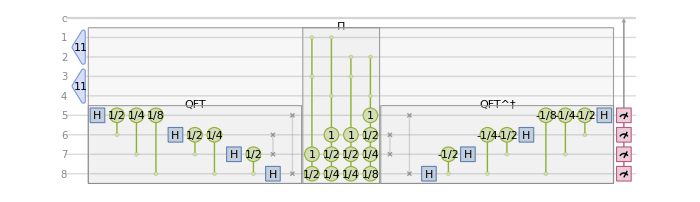

```mathematica
qc5=QuantumCircuitOperator[{
"11"->{1,2},
"11"->{3,4},
QuantumCircuitOperator[qftMul[2],"ShowLabel"->False],
"M"->{5,6,7,8}
}];
qc5["Diagram",ImageSize->700,Expand->2]
```

As expected, you get 9 with 100% probability when running this circuit:

```mathematica
N[qc5][]["Probability"]
```

<|1001→1.|>

You can define a function to check that this works in general:

```mathematica
Clear[checkercirc]
```

```mathematica
checkercirc=N@QuantumCircuitOperator[{
IntegerString[#1,2,2]->{1,2},
IntegerString[#2,2,2]->{3,4},
QuantumCircuitOperator[qftMul[2],"ShowLabel"->False],
"M"->{5,6,7,8}
}]&;
```

Apply the function to all integer pairs that can be expressed with two bits:

```mathematica
Grid[Table[ToString[i]<>"×"<>ToString[j]<>"="<>ToString[i*j]->First@Keys[checkercirc[i,j][]["Probability"]],{i,0,3},{j,0,3}],Spacings->{1,1},Frame->All]
```

0×0=0→0000 | 0×1=0→0000 | 0×2=0→0000 | 0×3=0→0000
1×0=0→0000 | 1×1=1→0001 | 1×2=2→0010 | 1×3=3→0011
2×0=0→0000 | 2×1=2→0010 | 2×2=4→0100 | 2×3=6→0110
3×0=0→0000 | 3×1=3→0011 | 3×2=6→0110 | 3×3=9→1001

As you can see, this circuit works as it should. You can also try with larger integers:

3×5=15

```mathematica
FromDigits[{0,1,1},2]FromDigits[{1,0,1},2]
```

15

Quantum circuit of multiplication:

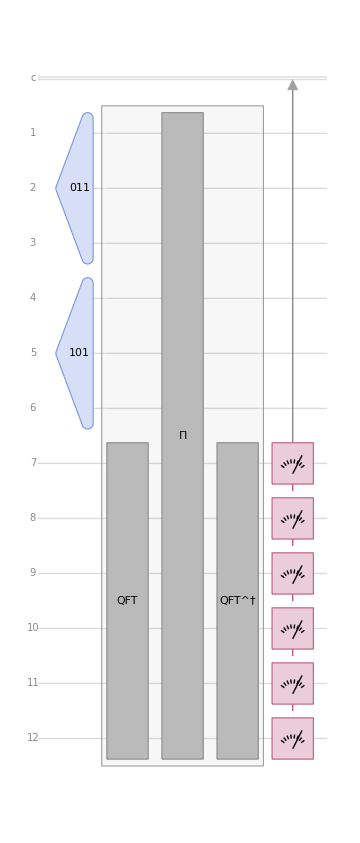

```mathematica
qc=Module[{n=3,qc},QuantumCircuitOperator[{
"011"->Range[n],
"101"->Range[n+1,2n],
QuantumCircuitOperator[qftMul[n],"ShowLabel"->False],
"M"->Range[2n+1,4n]
}]];
qc["Diagram"]
```

```mathematica
N[qc][]["Probability"]
```

<|001111→1.|>

Verify the result:

```mathematica
FromDigits[{0,0,1,1,1,1},2]
```

15

Notice that this implementation used double-controlled gates. If you need only 2-qubit gates for practical engineering reasons, the decomposition of the circuit will be more complicated.

## Finding Primes

Using the multiplication circuit, imagine the following experiment:

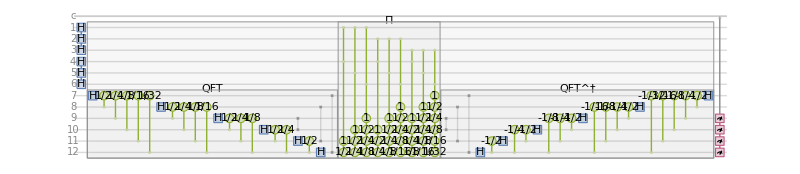

```mathematica
qc7=With[{n=3},QuantumCircuitOperator[{
"H"->Range[n],
"H"->Range[n+1,2n],
QuantumCircuitOperator[qftMul[n],"ShowLabel"->False],
"M"->Range[3n,4n]
}]];
qc7["Diagram",ImageSize->800,Expand->2]
```

The circuit above performs all multiplications of integers from 0 to 7. Then, the result modulo 16 is returned.

What happens if you simulated the measurements from this experiment? For this particular random seed, notice that you eventually discover “gaps” in the results which correspond to the primes 11 and 13. However, this particular method very nearly missed that 15 is composite, as the simulated experiment returned this result only once (due to randomness in the measurement outcomes).

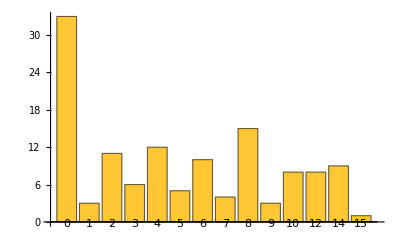

```mathematica
SeedRandom[321];
BarChart[
KeySort@CountsBy[
N[qc7][]["SimulatedMeasurement",128],
FromDigits[First@#,2]&
],ChartLabels->Automatic
]
```

## Initialization

Install Wolfram quantum framework

```mathematica
PacletInstall["https://www.wolfr.am/DevWQCF",ForceVersionInstall->True]
<<Wolfram`QuantumFramework`
```

PacletObject[…]

Define binAdd function:

```mathematica
binAdd[str1_String,str2_String]/;AllTrue[{str1,str2},StringFreeQ[Except["0"|"1"]..]]:=IntegerString[FromDigits[str1,2]+FromDigits[str2,2],2]
```